```mathematica
mx=MatrixForm;ft=Flatten;fs=FullSimplify;nls=Normal[Series[#1,#2]]&;AS=ApplySides;po=PowerExpand;
ℛ=Ramp;Θ=HeavisideTheta;op=Opacity;dsh=Dashed;AT=AbsoluteTiming;
LaunchKernels[];
```

## Preliminary (RUN ONCE)

### theory: Feller coefs from Hubbarde et al’s Burst-Death model with fixed burst size

#### Hubbarde et al (2007) results

-Graphics-

λ : burst  rate  (infection  cycle + between  cell  transport)
μ : death  rate  (loss  due  to  imunity, bottlenecks, denaturation  etc .)
B >= 2 : burst  size  (B = 2 : bacterial  division)
set  β = B - 1 = burst  size - 1

PGF of single type dynamics n_t: G[z,t]≡𝔼[z^n_t] for 0<z<=1
satisfies the PDE: 
∂_t G==(λ z^(β+1)-(λ+μ)z+μ)∂_z G

```mathematica
PGFeq=D[G[z,t], t]==(λ z^(β+1)-(λ+μ)z+μ)D[G[z,t], z]
```

G^(0,1)[z,t]==(z^(1+β) λ+μ-z (λ+μ)) G^(1,0)[z,t]

#### moments dynamics

PGF properties:
G^(1,0)[1,t]=X̄[t] and  G^(2,0)[1,t]+G^(1,0)[1,t]=OverBar[X^2][t]=𝕍_X[t]+(X̄[t])^2
so that
G^(1,1)[1,t]=X̄'[t]
G^(2,0)[1,t]=𝕍_X[t]+(X̄[t])^2-X̄[t]
G^(2,1)[1,t]=𝕍_X'[t]+2 X̄[t] X̄'[t]-X̄'[t]

```mathematica
{D[z^X, z],D[z^X, z]+D[z^X, z,z]}/.z->1//fs
D[Subscript[𝕍, X][t]+(X̄[t])^2-X̄[t],t]
convert={Derivative[1,1][G][1,t]->X̄'[t],Derivative[1,0][G][1,t]->X̄[t],Derivative[2,0][G][1,t]->Subscript[𝕍, X][t]+(X̄[t])^2-X̄[t],Derivative[2,1][G][1,t]->Subscript[𝕍, X]'[t]+2 X̄[t] X̄'[t]-X̄'[t]};
convert//mx
```

{X,X^2}

-X̄'[t]+2 X̄[t] X̄'[t]+𝕍_X'[t]

(G^(1,1)[1,t]→X̄'[t]
G^(1,0)[1,t]→X̄[t]
G^(2,0)[1,t]→-X̄[t]+(X̄[t])^2+𝕍_X[t]
G^(2,1)[1,t]→-X̄'[t]+2 X̄[t] X̄'[t]+𝕍_X'[t])

plug that into PGF equation to find ode solved by {X̄[t],𝕍_X[t]}

X̄'[t]==r X̄[t]
𝕍_X'[t]==σ X̄[t]+2 r 𝕍_X[t]
r=β λ-μ
σ=μ+β (r+μ)

```mathematica
fellercoefs=ft[Solve[{r==β λ-μ,σ==μ+β (r+μ)},{λ,μ}]];
eqX=AS[fs[D[#, z]/.z->1/.convert/.fellercoefs]&,PGFeq]
eqV=AS[fs[-2 X̄[t] X̄'[t]+D[#, z]+D[#, z,z]/.z->1/.convert/.X̄'[t]->r X̄[t]/.fellercoefs]&,PGFeq]
```

X̄'[t]==r X̄[t]

𝕍_X'[t]==σ X̄[t]+2 r 𝕍_X[t]

solve with IC fixed :X̄[0]==x_0 and 𝕍_X[0]==0
X̄[t]= x_0 ⅇ^(r t)
𝕍_X[t]=(σ x_0)/r ⅇ^(r t) (ⅇ^(r t)-1)

```mathematica
MVsol=ft[DSolve[{X̄'[t]==r X̄[t],Subscript[𝕍, X]'[t]==σ X̄[t]+2 r Subscript[𝕍, X][t],X̄[0]==Subscript[x, 0],Subscript[𝕍, X][0]==0},{X̄,Subscript[𝕍, X]},t]]
```

{X̄→Function[{t},ⅇ^(r t) x_0],𝕍_X→Function[{t},(ⅇ^(r t) (-1+ⅇ^(r t)) σ x_0)/r]}

take infinitesimal change in var and mean given fixed initial state to get Feller diffusion coefficients
infinitesimal growth rate r=β λ-μ
infintiesimal variance rate σ=μ+β (r+μ)

```mathematica
{r,σ}==Limit[{D[(X̄[t])/Subscript[x, 0], t],D[(Subscript[𝕍, X][t])/Subscript[x, 0], t]}/.MVsol,t->0]
```

True

we have that r/σ=r/(μ+β (r+μ))(->)_(β->∞
r,μ=O[1])0 as required for feller diffusion (r<<σ)

```mathematica
Limit[r/(μ+β (r+μ)),β->∞]
```

0

we claim that we can approximate the log establishment proba 1-ⅇ^(-2 r/σ) by that using a fixed σ0 in the host:1-ⅇ^(-2 r/σ0) 
check the difference between the two alternative exponents: Δ=r/σ-r/σ0
let relative mutant effects appear on life history traits β and μ and overall on r:
 {β->β_0(1+s_β ϵ),μ->μ_0(1+s_μ ϵ),r->r_0(1+𝓈 ϵ)}
let r0=1 (time rescaling)
with small selection coefs on all traits ϵ<<1 and large WT burst size  β_0=O[ϵ^-1]>>1:
the difference is of order :Δ ~ - ϵ^2 (𝓈+s_β+(s_β+s_μ) μ_0)/(β_0 (1+μ_0)^2)
so negligible at order of selection coefs ϵ

```mathematica
1/σ-1/σ0//.{σ->μ+β (r+μ),σ0->μ0+β0 (r0+μ0)}
%/.{r->r0(1+𝓈 ϵ),μ->μ0(1+Subscript[s, μ] ϵ),β->β0(1+Subscript[s, β] ϵ)}//fs
nls[%/.β0->β0/ϵ,{ϵ,0,2}]/.{r0->1,μ0->Subscript[μ, 0],β0->Subscript[β, 0]}//fs
```

1/(μ+β (r+μ))-1/(μ0+β0 (r0+μ0))

-1/(μ0+β0 (r0+μ0))+1/(μ0+ϵ μ0 s_μ+β0 (1+ϵ s_β) (r0+r0 𝓈 ϵ+μ0+ϵ μ0 s_μ))

-(ϵ^2 (𝓈+s_β+(s_β+s_μ) μ_0))/(β_0 (1+μ_0)^2)

### Code: 2 type Burst - Death algo (run once)

#### define rates

β_i=B_i-1 change in copy count upon burst for type i 
b_i: rate of burst of type i (intercell travel + within cell infection)\[Distributed]Exp[1/b_i]
d_i: rate of death of type i (waiting time to a viral particle killed or list)\[Distributed]Exp[1/d_i]

```mathematica
(* linear diagonal rates of each burst or death event*)
rates=Function[{x,pa},({{Subscript[b, 1] x[[1]]}, {Subscript[b, 2] x[[2]]}, {Subscript[d, 1] x[[1]]}, {Subscript[d, 2] x[[2]]}})//.pa];
(*effect of each event | ignoring mutation*)
Ε=Function[pa,({{Subscript[β, 1], 0}, {0, Subscript[β, 2]}, {-1, 0}, {0, -1}})//.pa];
```

when burst occurs in WT :B_1= β_1+1 viral copies are produced 
each copy is mutant with proba u and non mutant with proba 1-u
nb mutants produced by infecton :\[Distributed]Binomial[B_1,u]
no back mutation from mutant here by assumption

check rates  implementation  with  some  parameters

```mathematica
xs=Subscript[x, #]&/@Range[2];
pars=Thread/@{(Subscript[d, #]&/@Range[2])->0.2,(Subscript[β, #]&/@Range[2])->(BB-1){1,1},(Subscript[b, #]&/@Range[2])->{1/(BB-1),1.0/(BB-1)},u->0.01,BB->20,Subscript[x, 0]->10}//ft;
rates[xs,pars]//N//mx
Ε[pars]//mx
```

(0.0526316 x_1
0.0526316 x_2
0.2 x_1
0.2 x_2)

(19 | 0
0 | 19
-1 | 0
0 | -1)

#### define iteration function given parameters pa (to be defined later)

```mathematica
args=.;(*args={time,{Subscript[n, WT],Subscript[n, mutant]},parameters}*)
Iteration=Function[args,
Block[{ρ=rates[args[[2]],args[[3]]],pa=args[[3]],what,τ,newNM,newt,nm},
what=RandomChoice [ρ->Range[Length[ρ]]];
τ=RandomVariate[ExponentialDistribution[Total[ρ]]];
newt=args[[1]]+τ;
If[what==1,(*if birth of WT compute mutants*)
{nm=RandomVariate[BinomialDistribution[Subscript[β, what]+1//.pa,u//.pa]],newNM=args[[2]]+{Subscript[β, what]-nm,nm}//.pa},
newNM=args[[2]]+Ε[args[[3]]][[what]]];(*otherwise decoupled demography (+Subscript[β, i] or -1)*)

Sow[{newt,newNM[[1]],newNM[[2]]}];(*keep track of time, WT and mutant size*)
{newt,newNM,args[[3]]}
]
];
```

check  implementation  with  some  pars  and  initial  condition

```mathematica
pars=Thread/@{(Subscript[d, #]&/@Range[2])->0.0,(Subscript[β, #]&/@Range[2])->(BB-1){1,1},(Subscript[b, #]&/@Range[2])->{1/(BB-1),1.0/(BB-1)},u->0.2,BB->20,Subscript[x, 0]->10}//ft;
x0={10,0};Iteration[{0,x0,pars}]
```

{0.771464,{27,2},{d_1→0.,d_2→0.,β_1→-1+BB,β_2→-1+BB,b_1→1/(-1+BB),b_2→1./(-1+BB),u→0.2,BB→20,x_0→10}}

### Benchmark : check code behaviour

#### parameterize

set  burst + death  rates , burst  sizes, mutation  transition  probas  and  mutation  rate
so that WT birth rate (b_*(B_*-1)) is set to 1 and burst sizes scale with BB
here no mutation(u=0) and BB=2 (classic birth death)
growth rate : r_i=(B_i-1)b_i-d_i=b_i-d_i
initial  condition : {1,0}

```mathematica
pars=Thread/@{(Subscript[d, #]&/@Range[2])->0{0.1,0.12},(Subscript[β, #]&/@Range[2])->(BB-1){1,0.95},(Subscript[b, #]&/@Range[2])->{1,0.9}/(BB-1),u->0.0001,BB->50,Subscript[x, 0]->5,{Subscript[r, #]->Subscript[b, #] Subscript[β, #]-Subscript[d, #],Subscript[σ, #]->Subscript[d, #]+Subscript[β, #](Subscript[r, #]+Subscript[d, #])}&/@Range[2]}//ft;
x0={Subscript[x, 0],0}//.pars(*IC*)
{Subscript[b, #],Subscript[d, #],Subscript[β, #]}&/@Range[2]//.pars //N(*type demographic traits*)
{Subscript[r, #],Subscript[σ, #]}&/@Range[2]//.pars (*type growth rates*)
```

{5,0}

{{0.0204082,0.,49.},{0.0183673,0.,46.55}}

{{1.,49.},{0.855,39.8003}}

#### run one sim and plot it

run  simulation  until  n_t = Nmax

{0.0124425,Null}

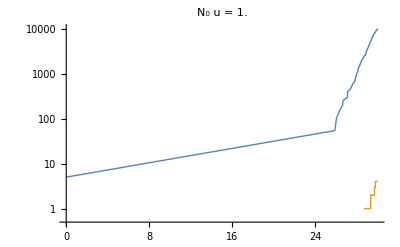

```mathematica
Nmax= 10^4; 
sim=Reap[NestWhile[Iteration,{0,x0,pars},0<Total[#[[2]]]<Nmax&]][[2,1]];//AT
PrependTo[sim,ft[{0,x0}]];(*add initial state state*)
Tmax=Max[sim[[All,1]]];nf=Last[sim][[2]];
ListLogPlot[{sim[[All,{1,2}]],sim[[All,{1,3}]]},Joined->True,PlotStyle->Thick,PlotRange->{{0,Tmax},{0.5,nf}},PlotLabel->StringForm["Ν_0 u = ``",Nmax u//.pars]]
```

to  make  a  proper  step plot for one sim

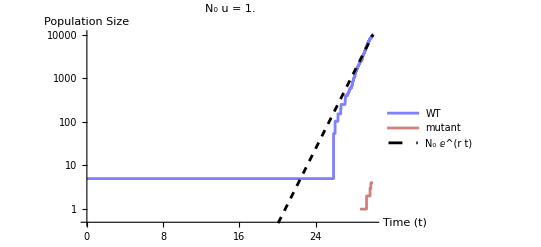

```mathematica
niceplot=Function[{data,format,lgd},Block[{stepData},
stepData=Flatten[Table[{{data[[i,1]],data[[i,2]]},{data[[i+1,1]],data[[i,2]]}},{i,1,Length[data]-1}],1];
(*Generate the exact horizontal and vertical corner points*)
stepData=Append[stepData,Last[data]];
ListLogPlot[stepData,AxesLabel->{"Time (t)","Population Size"},Joined->True,PlotStyle->{format},PlotLegends->lgd,PlotRange->{{0,Tmax},{0.5,nf}}]
]];
mutantdynplot=Show[niceplot[sim[[All,{1,2}]],{Blue,op[0.5]},Placed[LineLegend[{"WT"}],{0.2,0.8}]],niceplot[sim[[All,{1,3}]],{Darker[Red],op[0.5]},Placed[LineLegend[{"mutant"}],{0.23,0.7}]],LogPlot[Nmax ⅇ^(-Subscript[r, 1](Tmax-t))//.pars,{t,0,Tmax},PlotStyle->{{Dashed,Black}},PlotLegends->Placed[LineLegend[{"Ν_0 ⅇ^(r t)"}],{0.2,0.6}]],PlotLabel->StringForm["Ν_0 u = ``",Nmax u//.pars]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["MN_dynamics_SV_oither_example.pdf",mutantdynplot]
```

MN_dynamics_SV_oither_example.pdf

## Results and Checks : SV model Step 1

### mutant count distribution: B=2 (Benchmark = Lea Couslon theory)

```mathematica
pars=Thread/@{(Subscript[d, #]&/@Range[2])->{0,0},(Subscript[β, #]&/@Range[2])->(BB-1){1,1},(Subscript[b, #]&/@Range[2])->{1,1}/(BB-1),u->0.0001,BB->2,Subscript[x, 0]->10,{Subscript[r, #]->Subscript[b, #] Subscript[β, #]-Subscript[d, #],Subscript[σ, #]->Subscript[d, #]+Subscript[β, #](Subscript[r, #]+Subscript[d, #])}&/@Range[2]}//ft;
```

simulate in // stop when total pop reaches Nmax=N_0

```mathematica
nrep=14*500;Nmax=Round[0.1/u]//.pars;
sims0=ParallelTable[Reap[NestWhile[Iteration,{0,x0,pars},0<Total[#[[2]]]<Nmax&]][[2,1]],nrep];//AT
sims=Prepend[#,ft[{0,x0}]]&/@sims0;
```

{55.506,Null}

extract trajectories {t,m_t} for each rep (log-scale so only non zero trajectories)
pltot a subset

7.47815

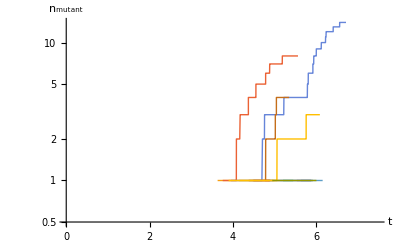

```mathematica
mutantrajectories=#[[All,{1,3}]]&/@sims;maxTs=Max[#[[All,1]]&/@sims]
ListLogPlot[mutantrajectories[[1;;Min[nrep,100]]],Joined->True,PlotStyle->Thick,PlotRange->{{0,maxTs},{0.5,All}},AxesLabel->{t,Subscript[n, mutant]}]
```

extract final mutant counts upon sampling (when total pop reaches N_0)

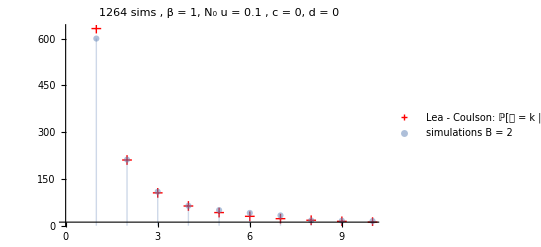

```mathematica
allcounts=(Last[#]&/@sims)[[All,3]]; (*all final m*)
mutantcounts=Select[allcounts,#>0&];(*those with at least one mutant*)
title=StringForm["`` sims , β = ``, N_0 u = `` , c = ``, d = ``",NumberForm[Length[mutantcounts]],NumberForm[Subscript[β, 1]//.pars],NumberForm[Nmax u//.pars],NumberForm[1-Subscript[r, 2]/Subscript[r, 1]//.pars],NumberForm[Subscript[d, 1]//.pars]];
 (*counts for each discrete m=k*)
kNk=Tally[mutantcounts];
leacoulsonplotPk=Show[DiscretePlot[Length[mutantcounts]/(k(k+1)),{k,0,10},Filling->None,Ticks->{Range[0,10],Automatic},PlotLabel->title,PlotStyle->{Red},PlotMarkers->"+",PlotRange->{{0,10},All},PlotLegends->Placed[LineLegend[{"Lea - Coulson: ℙ[𝓂 = k | k > 0] = 1/(k + SuperscriptBox[k, 2])"}],{0.6,0.8}]],ListPlot[kNk,Filling->Axis,PlotRange->{{0,10},All},Ticks->{Range[5],Automatic},PlotLabel->title,PlotStyle->op[0.5],PlotLegends->Placed[LineLegend[{StringForm["simulations B = ``",Subscript[β, 1]+1//.pars]}],{0.45,0.6}]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["LeaCoulsonPk.pdf",leacoulsonplotPk]
```

C:\Users\guillaume.martin\BOULOT SYNC\PROJETS EN COURS\SPECIAL_ISSUE_FITNESS_LANDSCAPE\multihost_ER_in_endives\simuls

LeaCoulsonPk.pdf

check proportion of pops that have no mutants vs basic theory ⅇ^(-b_1(Ν_0-x_0)u)

```mathematica
mutantcounts2=mutantcounts;Length[allcounts]==nrep
{ⅇ^(-Subscript[b, 1](Nmax -Subscript[x, 0])u)//.pars,1-Length[mutantcounts]/nrep}//N
```

True

{0.905743,0.819429}

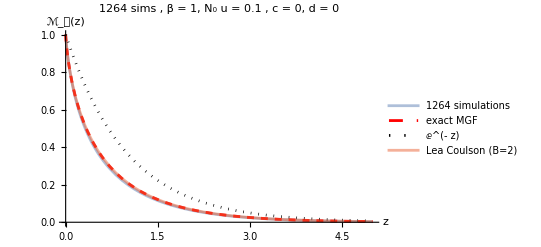

```mathematica
EMGF2=Function[z,Mean[ⅇ^(-mutantcounts2 z)]];
MGFth=(β X^(-1/β) Hypergeometric2F1[1/β,1/β+1/(1-c),1/β+(-2+c)/(-1+c),-1/X])/(1+β-c)/.X->ⅇ^(z β)-1/.{c->1-Subscript[r, 2]/Subscript[r, 1],β->Subscript[β, 1]}//.pars;
leacoulsonplotMGF=Plot[{EMGF2[z],MGFth,ⅇ^-z,1-(ⅇ^z-1) Log[1+1/(ⅇ^z-1)]},{z,0,5},PlotStyle->{op[0.5],{Dashed,Red},{Dotted,Black},op[0.5]},PlotLegends->LineLegend[{StringForm["`` simulations",NumberForm[Length[mutantcounts]]],"exact MGF","ⅇ^(- z)","Lea Coulson (B=2)"}],PlotLabel->title,PlotRange->{0,1},AxesLabel->{z,Subscript[ℳ, 𝓂][z]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["LeaCoulsonMGF.pdf",leacoulsonplotMGF]
```

C:\Users\guillaume.martin\BOULOT SYNC\PROJETS EN COURS\SPECIAL_ISSUE_FITNESS_LANDSCAPE\multihost_ER_in_endives\simuls

LeaCoulsonMGF.pdf

### mutant count distribution: B>>1 (our theory)

```mathematica
pars=Thread/@{(Subscript[d, #]&/@Range[2])->{0,0},(Subscript[β, #]&/@Range[2])->(BB-1){1,1},(Subscript[b, #]&/@Range[2])->{1,1}/(BB-1),u->0.0001,BB->21,Subscript[x, 0]->10,{Subscript[r, #]->Subscript[b, #] Subscript[β, #]-Subscript[d, #],Subscript[σ, #]->Subscript[d, #]+Subscript[β, #](Subscript[r, #]+Subscript[d, #])}&/@Range[2]}//ft;
```

simulate in // stop when total pop reaches Nmax=N_0

```mathematica
nrep=14*5000;Nmax=Round[0.1/u]//.pars;
sims0=ParallelTable[Reap[NestWhile[Iteration,{0,x0,pars},0<Total[#[[2]]]<Nmax&]][[2,1]],nrep];//AT
sims=Prepend[#,ft[{0,x0}]]&/@sims0;
```

{28.0314,Null}

extract trajectories {t,m_t} for each rep (log-scale so only non zero trajectories)
pltot a subset

48.0275

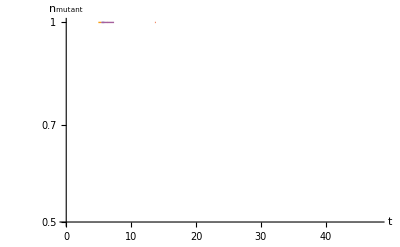

```mathematica
mutantrajectories=#[[All,{1,3}]]&/@sims;maxTs=Max[#[[All,1]]&/@sims]
ListLogPlot[mutantrajectories[[1;;Min[nrep,100]]],Joined->True,PlotStyle->Thick,PlotRange->{{0,maxTs},{0.5,All}},AxesLabel->{t,Subscript[n, mutant]}]
```

extract final mutant counts upon sampling (when total pop reaches N_0)

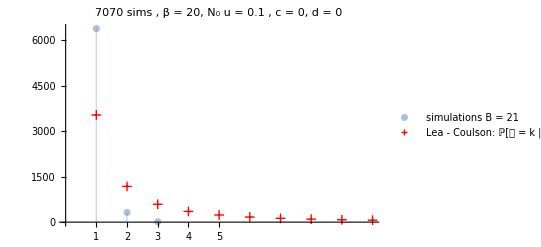

```mathematica
allcounts=(Last[#]&/@sims)[[All,3]]; (*all final m*)
mutantcounts=Select[allcounts,#>0&];(*those with at least one mutant*)
title=StringForm["`` sims , β = ``, N_0 u = `` , c = ``, d = ``",NumberForm[Length[mutantcounts]],NumberForm[Subscript[β, 1]//.pars],NumberForm[Nmax u//.pars],NumberForm[1-Subscript[r, 2]/Subscript[r, 1]//.pars],NumberForm[Subscript[d, 1]//.pars]];
 (*counts for each discrete m=k*)
kNk=Tally[mutantcounts];
plotPk=Show[ListPlot[kNk,Filling->Axis,PlotRange->{{0,10},All},Ticks->{Range[5],Automatic},PlotLabel->title,PlotStyle->op[0.5],PlotLegends->Placed[LineLegend[{StringForm["simulations B = ``",Subscript[β, 1]+1//.pars]}],{0.45,0.6}]],DiscretePlot[Length[mutantcounts]/(k(k+1)),{k,0,10},Filling->None,Ticks->{Range[0,10],Automatic},PlotLabel->title,PlotStyle->{Red},PlotMarkers->"+",PlotRange->{{0,10},All},PlotLegends->Placed[LineLegend[{"Lea - Coulson: ℙ[𝓂 = k | k > 0] = 1/(k + SuperscriptBox[k, 2])"}],{0.6,0.8}]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["B21Pk.pdf",plotPk]
```

C:\Users\guillaume.martin\BOULOT SYNC\PROJETS EN COURS\SPECIAL_ISSUE_FITNESS_LANDSCAPE\multihost_ER_in_endives\simuls

B21Pk.pdf

check proportion of pops that have no mutants vs. basic theory ⅇ^(-b_1 β_1(Ν_0-x_0)u)≈ⅇ^(-b_1 β_1 Ν_0 u)

```mathematica
mutantcounts21=mutantcounts;Length[allcounts]==nrep
{ⅇ^(-Subscript[b, 1] Subscript[β, 1] Nmax u)//.pars,1-Length[mutantcounts]/nrep}//N
```

True

{0.904837,0.899}

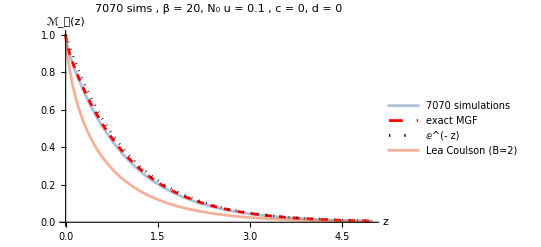

```mathematica
EMGF21=Function[z,Mean[ⅇ^(-mutantcounts21 z)]];
MGFth=(β X^(-1/β) Hypergeometric2F1[1/β,1/β+1/(1-c),1/β+(-2+c)/(-1+c),-1/X])/(1+β-c)/.X->ⅇ^(z β)-1/.{c->1-Subscript[r, 2]/Subscript[r, 1],β->Subscript[β, 1]}//.pars;
plotMGF=Plot[{EMGF21[z],MGFth,ⅇ^-z,1-(ⅇ^z-1) Log[1+1/(ⅇ^z-1)]},{z,0,5},PlotStyle->{op[0.5],{Dashed,Red},{Dotted,Black},op[0.5]},PlotLegends->LineLegend[{StringForm["`` simulations",NumberForm[Length[mutantcounts]]],"exact MGF","ⅇ^(- z)","Lea Coulson (B=2)"}],PlotLabel->title,PlotRange->{0,1},AxesLabel->{z,Subscript[ℳ, 𝓂][z]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["B21MGF.pdf",plotMGF]
```

C:\Users\guillaume.martin\BOULOT SYNC\PROJETS EN COURS\SPECIAL_ISSUE_FITNESS_LANDSCAPE\multihost_ER_in_endives\simuls

B21MGF.pdf

### mutant count distribution: B>>1 + cost 3% and some death (robustness of the theory)

```mathematica
pars=Thread/@{(Subscript[d, #]&/@Range[2])->{0.2,0.2},(Subscript[β, #]&/@Range[2])->(BB-1){1,1},(Subscript[b, #]&/@Range[2])->{1,0.975}/(BB-1),u->0.0001,BB->51,Subscript[x, 0]->10,{Subscript[r, #]->Subscript[b, #] Subscript[β, #]-Subscript[d, #],Subscript[σ, #]->Subscript[d, #]+Subscript[β, #](Subscript[r, #]+Subscript[d, #])}&/@Range[2]}//ft;
StringForm["with a cost c = `` and some death d_1 = d_2 = ``",NumberForm[1-Subscript[r, 2]/Subscript[r, 1]//.pars,2],Subscript[d, 1]//.pars]
```

with a cost c = 0.031 and some death d_1 = d_2 = 0.2

simulate in // stop when total pop reaches Nmax=N_0

```mathematica
nrep=14*5000;Nmax=Round[0.1/u]//.pars;
sims0=ParallelTable[Reap[NestWhile[Iteration,{0,x0,pars},0<Total[#[[2]]]<Nmax&]][[2,1]],nrep];//AT
sims=Prepend[#,ft[{0,x0}]]&/@sims0;
```

{46.2266,Null}

extract trajectories {t,m_t} for each rep (log-scale so only non zero trajectories)
pltot a subset

66.6095

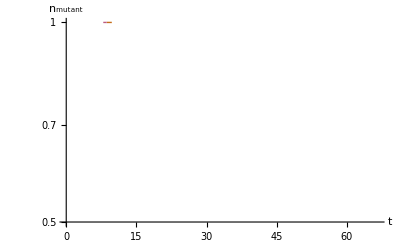

```mathematica
mutantrajectories=#[[All,{1,3}]]&/@sims;maxTs=Max[#[[All,1]]&/@sims]
ListLogPlot[mutantrajectories[[1;;Min[nrep,100]]],Joined->True,PlotStyle->Thick,PlotRange->{{0,maxTs},{0.5,All}},AxesLabel->{t,Subscript[n, mutant]}]
```

extract final mutant counts upon sampling (when total pop reaches N_0)

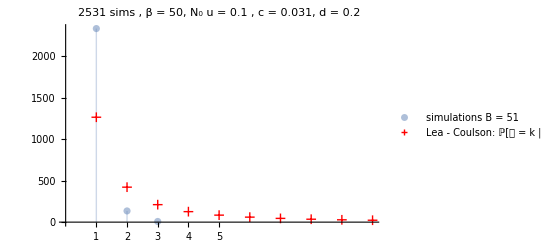

```mathematica
allcounts=(Last[#]&/@sims)[[All,3]]; (*all final m*)
mutantcounts=Select[allcounts,#>0&];(*those with at least one mutant*)
title=StringForm["`` sims , β = ``, N_0 u = `` , c = ``, d = ``",NumberForm[Length[mutantcounts]],NumberForm[Subscript[β, 1]//.pars],NumberForm[Nmax u//.pars],NumberForm[1-Subscript[r, 2]/Subscript[r, 1]//.pars,2],NumberForm[Subscript[d, 1]//.pars]];
 (*counts for each discrete m=k*)
kNk=Tally[mutantcounts];
plotPk=Show[ListPlot[kNk,Filling->Axis,PlotRange->{{0,10},All},Ticks->{Range[5],Automatic},PlotLabel->title,PlotStyle->op[0.5],PlotLegends->Placed[LineLegend[{StringForm["simulations B = ``",Subscript[β, 1]+1//.pars]}],{0.45,0.6}]],DiscretePlot[Length[mutantcounts]/(k(k+1)),{k,0,10},Filling->None,Ticks->{Range[0,10],Automatic},PlotLabel->title,PlotStyle->{Red},PlotMarkers->"+",PlotRange->{{0,10},All},PlotLegends->Placed[LineLegend[{"Lea - Coulson: ℙ[𝓂 = k | k > 0] = 1/(k + SuperscriptBox[k, 2])"}],{0.6,0.8}]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["B51CostDeathPk.pdf",plotPk]
```

C:\Users\guillaume.martin\BOULOT SYNC\PROJETS EN COURS\SPECIAL_ISSUE_FITNESS_LANDSCAPE\multihost_ER_in_endives\simuls

B51CostDeathPk.pdf

check proportion of pops that have no mutants vs. basic theory ⅇ^(-b_1 β_1(Ν_0-x_0)u)≈ⅇ^(-b_1 β_1 Ν_0 u)

```mathematica
mutantcounts51=mutantcounts;Length[allcounts]==nrep
{ⅇ^(-Subscript[b, 1] Subscript[β, 1] Nmax u)//.pars,1-Length[mutantcounts]/nrep}//N
```

True

{0.904837,0.963843}

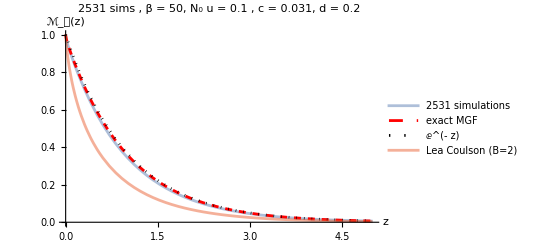

```mathematica
EMGF51=Function[z,Mean[ⅇ^(-mutantcounts51 z)]];
MGFth=(β X^(-1/β) Hypergeometric2F1[1/β,1/β+1/(1-c),1/β+(-2+c)/(-1+c),-1/X])/(1+β-c)/.X->ⅇ^(z β)-1/.{c->1-Subscript[r, 2]/Subscript[r, 1],β->Subscript[β, 1]}//.pars;
plotMGF=Plot[{EMGF51[z],MGFth,ⅇ^-z,1-(ⅇ^z-1) Log[1+1/(ⅇ^z-1)]},{z,0,5},PlotStyle->{op[0.5],{Dashed,Red},{Dotted,Black},op[0.5]},PlotLegends->LineLegend[{StringForm["`` simulations",NumberForm[Length[mutantcounts]]],"exact MGF","ⅇ^(- z)","Lea Coulson (B=2)"}],PlotLabel->title,PlotRange->{0,1},AxesLabel->{z,Subscript[ℳ, 𝓂][z]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["B51CostDeathMGF.pdf",plotMGF]
```

C:\Users\guillaume.martin\BOULOT SYNC\PROJETS EN COURS\SPECIAL_ISSUE_FITNESS_LANDSCAPE\multihost_ER_in_endives\simuls

B51CostDeathMGF.pdf

## Results and Checks : Feller approx step 2

### Burst Death process vs Feller approx

#### run // sims

```mathematica
pars=Thread/@{(Subscript[d, #]&/@Range[2])->{0.1,0.12},(Subscript[β, #]&/@Range[2])->(BB-1){1,1},(Subscript[b, #]&/@Range[2])->(1/Subscript[β, #]&/@Range[2]),u->0.0,BB->15,Subscript[x, 0]->10,{Subscript[r, #]->Subscript[b, #] Subscript[β, #]-Subscript[d, #],Subscript[σ, #]->Subscript[d, #]+Subscript[β, #](Subscript[r, #]+Subscript[d, #])}&/@Range[2]}//ft;
x0={Subscript[x, 0],0}//.pars(*IC*)
{Subscript[b, #],Subscript[d, #],Subscript[β, #]}&/@Range[2]//.pars //N(*type demographic traits*)
{Subscript[r, #],Subscript[σ, #]}&/@Range[2]//.pars (*type growth rates*)
```

{10,0}

{{0.0714286,0.1,14.},{0.0714286,0.12,14.}}

{{0.9,14.1},{0.88,14.12}}

```mathematica
nrep=14*2000;tmax=8;
sims0=ParallelTable[Reap[NestWhile[Iteration,{0,x0,pars},0<Total[#[[2]]]&&#[[1]]<tmax&]][[2,1]],nrep];//AT
sims=Prepend[#,ft[{0,x0}]]&/@sims0;
```

{815.294,Null}

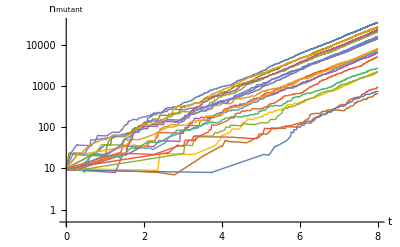

```mathematica
WTtrajectories=#[[All,{1,2}]]&/@sims;maxTs=tmax;
ListLogPlot[WTtrajectories[[1;;Min[nrep,20]]],Joined->True,PlotStyle->Thin,PlotRange->{{0,maxTs},{0.5,All}},AxesLabel->{t,Subscript[n, mutant]}]
```

#### extract simul data and check exact mean var dynamics

scaling  by  max  pop  size
set times where we plot the dist of n_t
create create interpolation function to extract replicate n’s at fixed times (DO NOT //IZE ! and use order 0 for precision)

```mathematica
𝒩=Max[sims[[All,2]]];
ts={0.8 tmax,tmax};
tns=Interpolation[#,InterpolationOrder->0]&/@WTtrajectories;//AT
```

{60.8918,Null}

```mathematica
title=StringForm["`` sims , β = ``,  b = ``, d = ``",NumberForm[Length[WTtrajectories]],NumberForm[Subscript[β, 1]//.pars],NumberForm[Subscript[b, 1]//.pars],NumberForm[Subscript[d, 1]//.pars]]
```

28000 sims , β = 14,  b = 1/14, d = 0.1

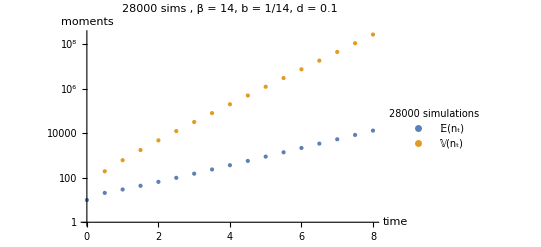

```mathematica
means=Prepend[Table[{t,Mean[#[t]&/@tns]}, {t,0.5,tmax,0.5}],{0,Subscript[x, 0]//.pars}];//Quiet
vars=Prepend[Table[{t,Variance[#[t]&/@tns]}, {t,0.5,tmax,0.5}],{0,0}];//Quiet
simplot=ListLogPlot[{means,vars},PlotStyle->PointSize[0.0075],PlotRange->{1,All},PlotLegends->Placed[LineLegend[{𝔼[Subscript[n, t]],𝕍[Subscript[n, t]]},LegendLabel->StringForm["`` simulations",nrep]],{0.2,0.8}],AxesLabel->{time,moments},PlotLabel->title]
```

solve the mean and variance dynamics analytically in terms of WT feller coefs r=r_1 and σ=σ_1
X̄'[t]==r X̄[t]
𝕍_X'[t]==σ X̄[t]+2 r 𝕍_X[t]

{X̄→Function[{t},ⅇ^(t r_1) x_0],𝕍_X→Function[{t},(ⅇ^(t r_1) (-1+ⅇ^(t r_1)) x_0 σ_1)/r_1]}

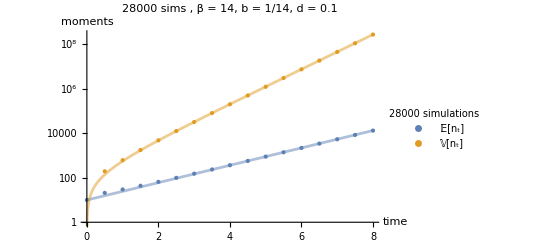

```mathematica
MVsol=ft[DSolve[{X̄'[t]==Subscript[r, 1] X̄[t],Subscript[𝕍, X]'[t]==Subscript[σ, 1] X̄[t]+2 Subscript[r, 1] Subscript[𝕍, X][t],X̄[0]==Subscript[x, 0],Subscript[𝕍, X][0]==0},{X̄,Subscript[𝕍, X]},t]]
momentplot=Show[simplot,LogPlot[Evaluate[{X̄[t],Subscript[𝕍, X][t]}/.MVsol//.pars],{t,0,tmax},PlotStyle->op[0.5],PlotLegends->Placed[LineLegend[{"",""},LegendLabel->Theory],{0.45,0.8}]]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["moment_check.pdf",momentplot]
```

moment_check.pdf

#### check feller dist approx

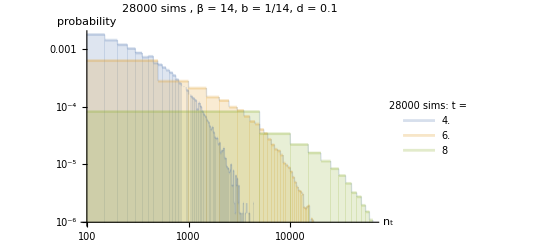

```mathematica
ts={0.5,0.75,1}tmax;𝒩=Max[#[tmax]&/@tns];//Quiet
𝒟s=HistogramDistribution/@(Function[t,#[t]&/@tns]/@ts);//Quiet
(*𝒟s=SmoothKernelDistribution/@(Function[t,(#[t])/𝒩&/@tns]/@ts);*)
simplot=LogLogPlot[Evaluate[PDF[#,𝓍]&/@𝒟s],{𝓍,10^2,10^5},PerformanceGoal->"Accuracy",Filling->Axis,PlotStyle->op[0.25],PlotRange->{10^-6,All},PlotLegends->Placed[LineLegend[ts,LegendLabel->StringForm["`` sims: t =",NumberForm[nrep]]],{0.75,0.8}],AxesLabel->{"n_t","probability"},PlotLabel->title]
```

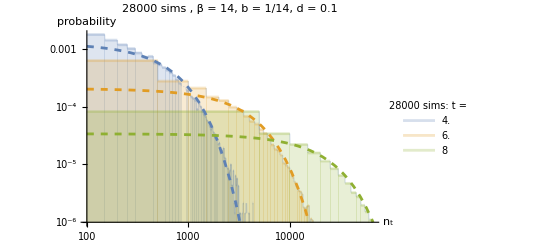

```mathematica
fellerpars={ν->(𝒸 Subscript[x, 0])/(1-ⅇ^(-Subscript[r, 1] t)),η->(ⅇ^(t Subscript[r, 1])-1)/𝒸,𝒸->(4 Subscript[r, 1])/Subscript[σ, 1]};
𝒻𝓍=(ⅇ^(-(𝓍+η ν)/(2 η)) ν Hypergeometric0F1[2,(𝓍 ν)/(4 η)])/(4 η);
theoryplot=LogLogPlot[Evaluate[𝒻𝓍//.fellerpars//.pars/.t->ts],{𝓍,10^2,10^5},PlotStyle->{{Dashed,Thick}},PlotRange->{10^-6,All},PlotLegends->Placed[LineLegend[{"","",""},LegendLabel->"Feller theory"],Top]];
pdfplot=Show[simplot,theoryplot]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Feller_check.pdf",pdfplot]
```

Feller_check.pdf